# pivotal MeSH

## PMID to MeSH rule

```mathematica
AbsoluteTiming[Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/mesh/PMIDtoMeSHDruleASC.save"];]
```

{96.0955,Null}

```mathematica
PMIDtoMeSHDruleASC//Head
```

Association

```mathematica
val=Values[PMIDtoMeSHDruleASC];
```

```mathematica
val//Length
```

30970332

## PMID vs pubyear

< year span >

```mathematica
yearrange=Partition[Table[ToString[n],{n,1946,2020}],5]
```

{{1946,1947,1948,1949,1950},{1951,1952,1953,1954,1955},{1956,1957,1958,1959,1960},{1961,1962,1963,1964,1965},{1966,1967,1968,1969,1970},{1971,1972,1973,1974,1975},{1976,1977,1978,1979,1980},{1981,1982,1983,1984,1985},{1986,1987,1988,1989,1990},{1991,1992,1993,1994,1995},{1996,1997,1998,1999,2000},{2001,2002,2003,2004,2005},{2006,2007,2008,2009,2010},{2011,2012,2013,2014,2015},{2016,2017,2018,2019,2020}}

< year span title >

```mathematica
yearrangetext=Map[#[[1]]<>"-"<>#[[5]]&,yearrange]
```

{1946-1950,1951-1955,1956-1960,1961-1965,1966-1970,1971-1975,1976-1980,1981-1985,1986-1990,1991-1995,1996-2000,2001-2005,2006-2010,2011-2015,2016-2020}

2 回目以降は以下を飛ばして下方のGetを実行する。

```mathematica
pubyearfiles=FileNames["/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyear*X.wl"]
```

{/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearTbl00X.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearTbl01X.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearTbl02X.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearTbl03X.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearTbl04X.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearTbl05X.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearTbl06X.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearTbl07X.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearTbl08X.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearTbl09X.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearTbl10X.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearTbl11X.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearTbl12X.wl}

```mathematica
(*AbsoluteTiming[(pubyearList=Association[Flatten[Map[Import,pubyearfiles]]])//Length]*)
```

```mathematica
pubyearList[["10004000"]]//Head
```

Part::pspec1: 部分指定10004000は適用できません．

Part

```mathematica
(*AbsoluteTiming[Do[
pubyear[yearrangetext[[n]]]=Select[pubyearList,MemberQ[yearrange[[n]],#]&];,{n,15}
]]*)
```

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearrule.save",pubyear]*)
```

2 回目以降は以下をGetする

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearrule.save"];
```

## Total count of appearance of MeSH (各年 => 累積)

PMID key の抽出

```mathematica
Do[
(pmidkey[yearrangetext[[n]]]=Keys[pubyear[yearrangetext[[n]]]])//Length,{n,15}
]
```

```mathematica
pmidkey[yearrangetext[[1]]][[1]]
```

12233288

PMIDからMeSHを引く

```mathematica
Do[
MeSHgenPre[yearrangetext[[n]]]=Map[PMIDtoMeSHDruleASC,pmidkey[yearrangetext[[n]]]],{n,15}
]
```

```mathematica
Table[Length[MeSHgenPre[yearrangetext[[n]]]],{n,15}]
```

{331362,534892,549642,725868,1014763,1166703,1352292,1542151,1917765,2144518,2393705,2971542,3776525,4953988,6062220}

```mathematica
MeSHgenPre["2016-2020"][[1]]
```

{Adolescent,Adult,Aged,Aged, 80 and over,Cheek,Coloring Agents,Ear Neoplasms,Facial Neoplasms,Facial Nerve,Facial Nerve Injuries,Female,Forehead,Humans,Lymph Node Excision,Lymphatic Metastasis,Lymphoscintigraphy,Male,Melanoma,Middle Aged,Neoplasm Recurrence, Local,Parotid Neoplasms,Parotid Region,Recovery of Function,Retrospective Studies,Sentinel Lymph Node,Sentinel Lymph Node Biopsy,Skin Neoplasms,Tumor Burden,Young Adult}

Missingをdrop

```mathematica
Do[
MeSHgen[yearrangetext[[n]]]=Cases[MeSHgenPre[yearrangetext[[n]]],x_/;Head[x]==List],{n,15}
]
```

```mathematica
Table[Length[MeSHgen[yearrangetext[[n]]]],{n,15}]
```

{319921,527332,538750,709330,987502,1138604,1317387,1484633,1813556,2002399,2229534,2777961,3434594,4190064,4479011}

### 延べカウント

<各世代のカウント>

```mathematica
MeSHflatcount=Table[Flatten[MeSHgen[yearrangetext[[n]]]]//Length,{n,15}]
```

{1260830,2405880,2550730,4831845,8429174,11935276,11955149,14373206,17562197,21776471,25912004,33165585,40830011,49634377,50404722}

<累積世代のカウント>

```mathematica
MeSHflatcountAcm=Accumulate[MeSHflatcount]
```

{1260830,3666710,6217440,11049285,19478459,31413735,43368884,57742090,75304287,97080758,122992762,156158347,196988358,246622735,297027457}

### タームカウント

各世代のTally

```mathematica
(MeSHflatcountTly=Table[Flatten[MeSHgen[yearrangetext[[n]]]]//Tally,{n,15}])//Length
```

15

```mathematica
MeSHflatcountTly[[1]]
```

累積世代のTally

```mathematica
tallyInteg[l_]:=If[Length[l]>=1,
{l[[1,1]],Total[Map[#[[2]]&,l]]},
l
]
```

```mathematica
(MeSHacmcountTly=Table[Map[tallyInteg,GatherBy[Apply[Join,MeSHflatcountTly[[1;;n]]],First]],{n,15}])//Length
```

15

<累積世代のディスクリプターのカウント>

```mathematica
MeSHDesccountAcm=Map[Length,MeSHacmcountTly]
```

{13448,15858,17483,19065,19489,20449,21492,22288,23304,24817,25954,27076,27881,28767,29898}

```mathematica
MeSHacmcountTly[[1]][[1]]
```

{Contraception,87}

### 重みつきタームカウント

MeSHgenを分数カウントする（一旦ペンディング）

```mathematica
MeSHgen[yearrangetext[[1]]]//Length
```

319921

## Pivotal count of appearance of MeSH (各年 => 累積)

### 主要論文

変数: topCitingCitedArt1Perc[YYYY, "citing rule"]

```mathematica
mainartfiles=Table["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-"<>ToString[n]<>"_topCitingCitedArt1Perc.save",{n,1950,2020,5}]
```

{/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1950_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1955_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1960_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1965_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1970_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1975_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1980_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1985_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1990_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1995_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2000_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2005_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2010_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2015_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2020_topCitingCitedArt1Perc.save}

```mathematica
Map[Get,mainartfiles];
```

```mathematica
mainartPMIDgen=Table[Map[#[[2]]&,topCitingCitedArt1Perc[n, "citing rule"],{2}]//Flatten//Union,{n,1950,2020,5}];
```

```mathematica
mainartPMIDgen[[2,1]]
```

14772207

```mathematica
PMIDtoMeSHDruleASC[mainartPMIDgen[[2,1]]]
```

{Blood Proteins,Electrophoresis,Filtration}

### 主要MeSH

PMIDからMeSHを引く

```mathematica
(mainMeSHgen=DeleteCases[Map[PMIDtoMeSHDruleASC,mainartPMIDgen,{-1}],_Missing,Infinity])//Length
```

15

### 延べカウント

```mathematica
mainMeSHflatcountAcm=Map[Length[Flatten[#]]&,mainMeSHgen]
```

{0,56,139,192,194,189,199,220,162,202,321,637,2008,3462,3613}

### タームカウント

```mathematica
mainMeSHgen[[2]]
```

{{Blood Proteins,Electrophoresis,Filtration},{Blood,Blood Proteins,Electrophoresis,Proteins},{Molybdenum,Phenols,Plant Extracts,Proteins,Tungsten Compounds},{Anemia,Anemia, Sickle Cell,Humans},{Chromatography,Chromatography, Paper,Esters,Filtration,Phosphorus,Phosphorus Compounds,Rare Diseases},{Humans,Salts},{Acclimatization,Adaptation, Physiological,Humans,Metabolic Networks and Pathways,Metabolism},{Brain,Cerebrovascular Circulation,Humans,Male,Nitrous Oxide,Reference Values},{Cytochromes,Cytochromes c},{Insulin},{Complex Mixtures,Humans,Identification, Psychological,Peptides},{Adrenal Glands,Epinephrine,Tissue Extracts},{Capillaries,Chromatography,Chromatography, Paper,Humans},{Animals,Axons,Decapodiformes,Ions,Neurons,Sodium,Sodium, Dietary}}

```mathematica
(mainMeSHflatcountTly=Map[Tally[Flatten[#]]&,mainMeSHgen])//Length
```

15

```mathematica
mainMeSHgencount=Map[Length,mainMeSHflatcountTly]
```

{0,45,96,117,122,125,137,143,108,128,199,325,875,1243,1178}

### 新規出現

すでに累積になっているので前世代との差分をとる。

```mathematica
mainMeSHgenflatt=Map[Flatten[#]&,mainMeSHgen];
```

```mathematica
mainMeSHgendiff=Table[Complement[mainMeSHgenflatt[[n+1]],mainMeSHgenflatt[[n]]],{n,14}];
```

```mathematica
mainMeSHgennewcomercount=Prepend[Map[Length,mainMeSHgendiff],0]
```

{0,45,61,42,33,21,44,55,9,30,71,126,550,468,217}

## Plot

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/exec_command/generations.wl"]
```

{1950,1955,1960,1965,1970,1975,1980,1985,1990,1995,2000,2005,2010,2015,2020}

```mathematica
ListPlot[{mainMeSHflatcountAcm,mainMeSHgennewcomercount},Joined->True,PlotRange->Full,Frame->True,FrameTicks->{Automatic,{genticks,None}},PlotLabels->{"主要\nディスクリプター数","新規出現主要\nディスクリプター数"}]
```

-Graphics-

```mathematica
mainMeSHgennewcomercount/mainMeSHflatcountAcm/.Indeterminate->0
```

Power::infy: 無限式1/0が見付かりました．

Infinity::indet: 不定式0 ComplexInfinityが見付かりました．

{0,45/56,61/139,7/32,33/194,1/9,44/199,1/4,1/18,15/101,71/321,18/91,275/1004,78/577,217/3613}

Power::infy: 無限式1/0が見付かりました．

Infinity::indet: 不定式0 ComplexInfinityが見付かりました．

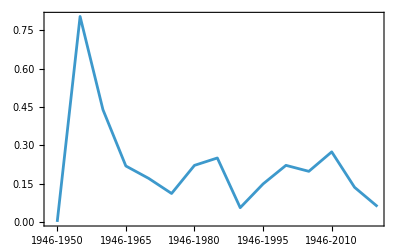
-Graphics-新規出現主要ディスクリプターの主要ディスクリプターに占める割合（%）

```mathematica
Labeled[ListPlot[mainMeSHgennewcomercount/mainMeSHflatcountAcm/.Indeterminate->0,Joined->True,PlotRange->Full,Frame->True,FrameTicks->{Automatic,{genticks,None}}],"新規出現主要ディスクリプターの主要ディスクリプターに占める割合（%）"]
```

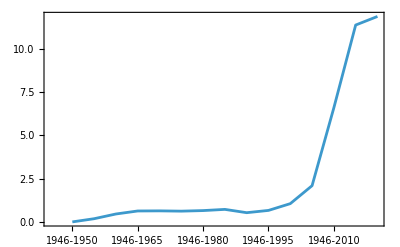
-Graphics-主要ディスクリプターの全ディスクリプターに占める割合（%）
注) 全ディスクリプター数は2023年のMeSH登録数より求めたもので、
全世代を通して同数である。

```mathematica
Labeled[ListPlot[mainMeSHflatcountAcm/30454*100,Joined->True,Frame->True,FrameTicks->{Automatic,{genticks,None}}],"主要ディスクリプターの全ディスクリプターに占める割合（%）\n注) 全ディスクリプター数は2023年のMeSH登録数より求めたもので、\n全世代を通して同数である。"]
```